# Unit 3 · Attention, Part by Part

## The transformer built from plain arrays and from primitive layers (Vaswani et al., 2017) — TensorNets units of learning, 3 of 4

© 2026 Computational Classnotes · CC BY-NC-SA 4.0

The transformer drops recurrence. Every word looks at every other word at once, through attention, and position is added as a code. This unit builds each part twice: from plain arrays, to see the mathematics, and as a Wolfram net from primitive layers, to train it. Each section checks that the two agree. Evaluate from top to bottom; it takes about a minute. The write-up “Unit 3 · Attention, Part by Part” has the same section numbers.

Before you start: choose Evaluation ▸ Quit Kernel ▸ Local.

## 1. Toolkit

Arrays first: softmaxRows, sdpa (scaled dot-product attention, §3), the masks (§5), mha (§6), pe (§7), ffn and layerNorm (§8), encoderLayer and decoderLayer (§9). Then the same parts as nets built from primitive layers: mhaNet, peNet, ffnNet, encoderLayerNet, decoderLayerNet. The array versions read their weights out of the nets, so the two can be compared exactly. Last, the training and decoding recipes: smoothTarget (§11), warmRate (§12), lengthPenalty (§13) and the parameter counts (§14).

```mathematica
(* id: 14d80494-f524-4883-8666-1bb5c883546a · unit3_transformer · cell 1 of 24 · updated 2026-11-24 06:58 UTC *)
close[a_, b_, tol_ : 10^-5] := Max[Abs[Flatten[{a - b}]]] < tol;
softmaxRows[m_] := Map[With[{e = Exp[# - Max[#]]}, e/Total[e]] &, m];
sdpa[q_, k_, v_, mask_ : None] := Module[{s = q . Transpose[k]/Sqrt[N@Last@Dimensions[k]]}, If[mask =!= None, s = s + mask]; softmaxRows[s] . v];
causalMask[n_Integer] := Table[If[j > i, -10.^9, 0.], {i, n}, {j, n}];
padMask[nq_Integer, nk_Integer, valid_Integer] := Table[If[j > valid, -10.^9, 0.], {nq}, {j, nk}];
(* multi-head attention as a net: projections, split into h heads, attention, join, projection *)
mhaNet[d_Integer, h_Integer, causal_ : False] := NetGraph[<|
    "q" -> NetMapOperator[LinearLayer[d]], "k" -> NetMapOperator[LinearLayer[d]], "v" -> NetMapOperator[LinearLayer[d]],
    "rq" -> NetMapOperator[ReshapeLayer[{h, d/h}]], "rk" -> NetMapOperator[ReshapeLayer[{h, d/h}]], "rv" -> NetMapOperator[ReshapeLayer[{h, d/h}]],
    "att" -> If[TrueQ[causal], AttentionLayer["Dot", "MultiHead" -> True, "ScoreRescaling" -> "DimensionSqrt", "Mask" -> "Causal"],
      AttentionLayer["Dot", "MultiHead" -> True, "ScoreRescaling" -> "DimensionSqrt"]],
    "cat" -> NetMapOperator[FlattenLayer[]], "o" -> NetMapOperator[LinearLayer[d]]|>,
   {NetPort["Query"] -> "q" -> "rq" -> NetPort["att", "Query"], NetPort["Memory"] -> "k" -> "rk" -> NetPort["att", "Key"],
    NetPort["Memory"] -> "v" -> "rv" -> NetPort["att", "Value"], "att" -> "cat" -> "o"},
   "Query" -> {"Varying", d}, "Memory" -> {"Varying", d}];
(* the same from arrays, reading the weights out of the net at the given path *)
linear[net_, path_List][x_] := With[{w = Normal@NetExtract[net, Join[path, {"Net", "Weights"}]], b = Normal@NetExtract[net, Join[path, {"Net", "Biases"}]]},
   x . Transpose[w] + ConstantArray[b, Length[x]]];
mha[net_, path_List, h_Integer, causal_ : False][x_, m_] := Module[{q, k, v, d, heads},
   q = linear[net, Append[path, "q"]][x]; k = linear[net, Append[path, "k"]][m]; v = linear[net, Append[path, "v"]][m]; d = Last@Dimensions[q];
   heads = Table[sdpa[q[[All, idx]], k[[All, idx]], v[[All, idx]], If[TrueQ[causal], causalMask[Length[x]], None]], {idx, Partition[Range[d], d/h]}];
   linear[net, Append[path, "o"]][Flatten /@ Transpose[heads, {2, 1, 3}]]];
(* sinusoidal positions; cos x = sin(x + π/2), so every component is sin(pos ω + φ) *)
freq[d_Integer] := Flatten@Table[{1., 1.}/10000.^(2 i/d), {i, 0, d/2 - 1}];
phase[d_Integer] := Table[If[EvenQ[j], 0., N[Pi/2]], {j, 0, d - 1}];
pe[n_Integer, d_Integer] := Table[Sin[pos freq[d] + phase[d]], {pos, 0, n - 1}];
peNet[d_Integer] := NetGraph[<|"idx" -> SequenceIndicesLayer[], "pos" -> ElementwiseLayer[# - 1. &], "col" -> ReplicateLayer[1, 2],
    "angle" -> NetMapOperator[LinearLayer[d, "Weights" -> List /@ freq[d], "Biases" -> phase[d], LearningRateMultipliers -> 0]],
    "sin" -> ElementwiseLayer[Sin], "add" -> TotalLayer[]|>,
   {NetPort["Input"] -> "idx" -> "pos" -> "col" -> "angle" -> "sin", {NetPort["Input"], "sin"} -> "add"}, "Input" -> {"Varying", d}];
shiftMatrix[k_, d_Integer] := Module[{w = freq[d][[1 ;; ;; 2]], m = ConstantArray[0., {d, d}]},
   Do[m[[2 i - 1 ;; 2 i, 2 i - 1 ;; 2 i]] = {{Cos[k w[[i]]], Sin[k w[[i]]]}, {-Sin[k w[[i]]], Cos[k w[[i]]]}}, {i, Length[w]}]; m];
(* feed-forward and layer normalisation *)
ffnNet[d_Integer, dff_Integer] := NetMapOperator[NetChain[{LinearLayer[dff], Ramp, LinearLayer[d]}], "Input" -> {"Varying", d}];
ffn[net_, path_List][x_] := Module[{w1, b1, w2, b2},
   {w1, b1, w2, b2} = Normal@NetExtract[net, Join[path, #]] & /@ {{"Net", 1, "Weights"}, {"Net", 1, "Biases"}, {"Net", 3, "Weights"}, {"Net", 3, "Biases"}};
   Map[w2 . Ramp[w1 . # + b1] + b2 &, x]];
layerNorm[net_, path_List][x_] := Module[{γ = Normal@NetExtract[net, Append[path, "Scaling"]], β = Normal@NetExtract[net, Append[path, "Biases"]], ε = NetExtract[net, Append[path, "Epsilon"]]},
   Map[γ (# - Mean[#])/Sqrt[Mean[(# - Mean[#])^2] + ε] + β &, x]];
(* one encoder layer and one decoder layer, as nets and from arrays *)
encoderLayerNet[d_Integer, h_Integer, dff_Integer] := NetGraph[<|
    "att" -> mhaNet[d, h], "add1" -> TotalLayer[], "ln1" -> NormalizationLayer[2, 2], "ffn" -> ffnNet[d, dff], "add2" -> TotalLayer[], "ln2" -> NormalizationLayer[2, 2]|>,
   {NetPort["Input"] -> NetPort["att", "Query"], NetPort["Input"] -> NetPort["att", "Memory"], {NetPort["Input"], "att"} -> "add1" -> "ln1" -> "ffn", {"ln1", "ffn"} -> "add2" -> "ln2"},
   "Input" -> {"Varying", d}];
decoderLayerNet[d_Integer, h_Integer, dff_Integer] := NetGraph[<|
    "self" -> mhaNet[d, h, True], "add1" -> TotalLayer[], "ln1" -> NormalizationLayer[2, 2],
    "cross" -> mhaNet[d, h], "add2" -> TotalLayer[], "ln2" -> NormalizationLayer[2, 2],
    "ffn" -> ffnNet[d, dff], "add3" -> TotalLayer[], "ln3" -> NormalizationLayer[2, 2]|>,
   {NetPort["Input"] -> NetPort["self", "Query"], NetPort["Input"] -> NetPort["self", "Memory"], {NetPort["Input"], "self"} -> "add1" -> "ln1",
    "ln1" -> NetPort["cross", "Query"], NetPort["Memory"] -> NetPort["cross", "Memory"], {"ln1", "cross"} -> "add2" -> "ln2" -> "ffn", {"ln2", "ffn"} -> "add3" -> "ln3"},
   "Input" -> {"Varying", d}, "Memory" -> {"Varying", d}];
encoderLayer[net_, h_][x_] := Module[{x1 = layerNorm[net, {"ln1"}][x + mha[net, {"att"}, h][x, x]]}, layerNorm[net, {"ln2"}][x1 + ffn[net, {"ffn"}][x1]]];
decoderLayer[net_, h_][y_, mem_] := Module[{y1, y2},
   y1 = layerNorm[net, {"ln1"}][y + mha[net, {"self"}, h, True][y, y]];
   y2 = layerNorm[net, {"ln2"}][y1 + mha[net, {"cross"}, h][y1, mem]];
   layerNorm[net, {"ln3"}][y2 + ffn[net, {"ffn"}][y2]]];
(* training and decoding recipes *)
smoothTarget[k_Integer, K_Integer, ε_ : 0.1] := ConstantArray[ε/K, K] + (1 - ε) UnitVector[K, k];
crossEntropy[q_, p_] := -q . Log[p];
warmRate[step_?NumericQ, d_ : 512, warmup_ : 4000] := d^-0.5 Min[step^-0.5, step warmup^-1.5];
lengthPenalty[len_, α_ : 0.6] := ((5 + len)/6.)^α;
mhaParams[d_Integer] := 4 (d d + d);
layerParams[d_, dff_] := <|"attention" -> mhaParams[d], "FFN" -> d dff + dff + dff d + d, "LayerNorm" -> 2 d|>;
SeedRandom[2017];
```

## 2. The idea: attention instead of recurrence

An LSTM (Unit 1) reads one word after another, so the first word reaches the last only through every step between them, and the steps cannot run in parallel. The transformer lets every position look at every other position directly. Each position asks a question (its query), every position offers an answer key and a value, and the output is an average of the values weighted by how well the keys match the query. Order is added as a position code.

The paper’s model is an encoder–decoder like Unit 1’s, with each LSTM replaced by a stack of layers built from attention and a small feed-forward network:

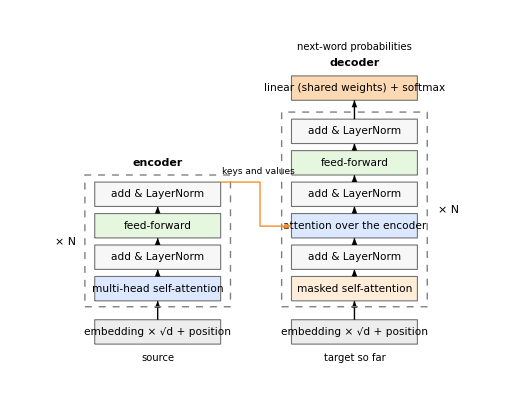

```mathematica
(* id: eaaf5389-6ddf-4d19-b99a-236fbec4f5b8 · unit3_transformer · cell 2 of 24 · updated 2026-11-24 06:58 UTC *)
blk[{x_, y_}, lab_, col_] := {EdgeForm[GrayLevel[0.45]], col, Rectangle[{x, y}, {x + 3.2, y + 0.62}], Black, Text[Style[lab, 10.5], {x + 1.6, y + 0.31}]};
up[x_, y1_, y2_] := Arrow[{{x, y1}, {x, y2}}];
Graphics[{Arrowheads[0.02],
  blk[{0, 0}, "embedding × √d + position", GrayLevel[0.93]], up[1.6, 0.62, 1.1],
  blk[{0, 1.1}, "multi-head self-attention", RGBColor[0.86, 0.91, 1]], up[1.6, 1.72, 1.9], blk[{0, 1.9}, "add & LayerNorm", GrayLevel[0.97]],
  up[1.6, 2.52, 2.7], blk[{0, 2.7}, "feed-forward", RGBColor[0.9, 0.97, 0.88]], up[1.6, 3.32, 3.5], blk[{0, 3.5}, "add & LayerNorm", GrayLevel[0.97]],
  {Dashed, GrayLevel[0.5], Line[{{-0.25, 0.95}, {3.45, 0.95}, {3.45, 4.3}, {-0.25, 4.3}, {-0.25, 0.95}}]}, Text[Style["× N", 11, Italic], {-0.75, 2.6}],
  Text[Style["encoder", Bold, 11], {1.6, 4.6}],
  blk[{5, 0}, "embedding × √d + position", GrayLevel[0.93]], up[6.6, 0.62, 1.1],
  blk[{5, 1.1}, "masked self-attention", RGBColor[1, 0.93, 0.85]], up[6.6, 1.72, 1.9], blk[{5, 1.9}, "add & LayerNorm", GrayLevel[0.97]],
  up[6.6, 2.52, 2.7], blk[{5, 2.7}, "attention over the encoder", RGBColor[0.86, 0.91, 1]], up[6.6, 3.32, 3.5], blk[{5, 3.5}, "add & LayerNorm", GrayLevel[0.97]],
  up[6.6, 4.12, 4.3], blk[{5, 4.3}, "feed-forward", RGBColor[0.9, 0.97, 0.88]], up[6.6, 4.92, 5.1], blk[{5, 5.1}, "add & LayerNorm", GrayLevel[0.97]],
  {Dashed, GrayLevel[0.5], Line[{{4.75, 0.95}, {8.45, 0.95}, {8.45, 5.9}, {4.75, 5.9}, {4.75, 0.95}}]}, Text[Style["× N", 11, Italic], {9, 3.4}],
  up[6.6, 5.72, 6.2], blk[{5, 6.2}, "linear (shared weights) + softmax", RGBColor[0.99, 0.85, 0.7]],
  Text[Style["decoder", Bold, 11], {6.6, 7.15}],
  {RGBColor[0.98, 0.56, 0.17], Thick, Arrow[{{3.2, 4.12}, {4.2, 4.12}, {4.2, 3.0}, {5, 3.0}}]}, Text[Style["keys and values", 9], {4.15, 4.4}],
  Text[Style["source", 10, Italic], {1.6, -0.35}], Text[Style["target so far", 10, Italic], {6.6, -0.35}], Text[Style["next-word probabilities", 10, Italic], {6.6, 7.55}]},
 ImageSize -> 520, PlotRange -> {{-1.2, 9.6}, {-0.7, 7.8}}]
```

Fig. 1. The transformer. Each encoder layer is self-attention then a feed-forward network, each wrapped as add & LayerNorm. Each decoder layer adds masked self-attention and attention over the encoder’s output (orange arrow). The paper uses N = 6.

## 3. Scaled dot-product attention

Stack the queries as rows of Q, the keys as rows of K and the values as rows of V. Compare every query with every key by a dot product, divide by √dₖ (§4), take the softmax of each row and average the values with those weights (Section 3.2.1 of the paper):

Attention(Q, K, V) = softmax( Q Kᵀ / √dₖ ) V

### 3.1 Worked by hand: one query, two keys

Let q = (1, 0), with keys k₁ = (1, 0), k₂ = (0, 1) and values v₁ = (1, 0), v₂ = (0, 1); dₖ = 2. The scores are q·k₁/√2 = 0.7071 and q·k₂/√2 = 0. The softmax weights are e^0.7071/(e^0.7071 + 1) = 2.028/3.028 = 0.670 and 1/3.028 = 0.330. The output is 0.670 v₁ + 0.330 v₂ = (0.670, 0.330): mostly the value of the matching key.

```mathematica
(* id: 8dc2abc4-48cf-4bad-b470-95584f003c0c · unit3_transformer · cell 3 of 24 · updated 2026-11-24 06:58 UTC *)
sdpa[{{1., 0.}}, {{1., 0.}, {0., 1.}}, {{1., 0.}, {0., 1.}}]
```

{{0.669762,0.330238}}

Check: {{0.670, 0.330}}.

```mathematica
(* id: ffb327ce-ab65-4dca-9322-0582e5decfe2 · unit3_transformer · cell 4 of 24 · updated 2026-11-24 06:58 UTC *)
q = RandomReal[{-1, 1}, {4, 6}]; k = RandomReal[{-1, 1}, {7, 6}]; v = RandomReal[{-1, 1}, {7, 3}];
{close[sdpa[q, k, v], AttentionLayer["Dot", "ScoreRescaling" -> "DimensionSqrt"][<|"Query" -> q, "Key" -> k, "Value" -> v|>]],
 close[Total[softmaxRows[q . Transpose[k]/Sqrt[6.]], {2}], ConstantArray[1., 4], 10^-12]}
```

{True,True}

Check: {True, True}. The formula coded from arrays equals Wolfram’s AttentionLayer with "ScoreRescaling" -> "DimensionSqrt" (4 queries, 7 keys), and every row of weights sums to 1.

## 4. Why divide by √dₖ

If the components of q and k are independent with mean 0 and variance 1, their dot product has mean 0 and variance dₖ (footnote 4 of the paper). For dₖ = 64 the scores are then about ±8, the softmax is close to one-hot, and its gradient is tiny. Dividing by √dₖ brings the variance back to 1.

q·k = q₁k₁ + … + q_d k_d is a sum of dₖ independent terms, each with mean 0 and variance E[q.b2]E[k.b2] = 1. Variances of independent terms add, so Var(q·k) = dₖ, and Var(q·k/√dₖ) = dₖ/dₖ = 1.

```mathematica
(* id: f9f0e5f9-6a04-4439-9b45-f15e16102eaf · unit3_transformer · cell 5 of 24 · updated 2026-11-24 06:58 UTC *)
qs = RandomVariate[NormalDistribution[], {20000, 64}]; ks = RandomVariate[NormalDistribution[], {20000, 64}];
dots = Total[qs ks, {2}];
{Variance[dots], Variance[dots/8.]}
```

{63.6303,0.994224}

Check: about {64, 1}.

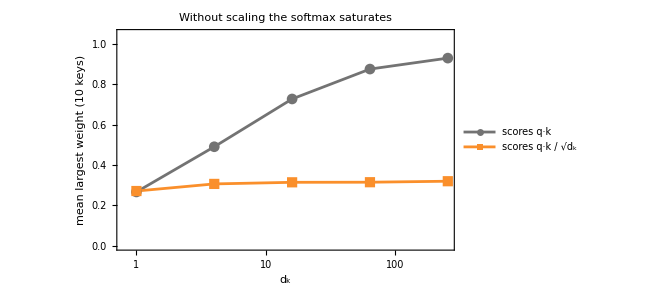

```mathematica
(* id: c0341c37-ad3c-4257-88b5-82ef00460e4b · unit3_transformer · cell 6 of 24 · updated 2026-11-24 06:58 UTC *)
largest[d_, scale_] := Mean@Table[Max@softmaxRows[{RandomVariate[NormalDistribution[], d] . Transpose[RandomVariate[NormalDistribution[], {10, d}]]/scale}], {1500}];
dims = {1, 4, 16, 64, 256};
sat = Table[{largest[d, 1.], largest[d, Sqrt[N@d]]}, {d, dims}];
ListLogLinearPlot[{Transpose[{dims, sat[[All, 1]]}], Transpose[{dims, sat[[All, 2]]}]}, Joined -> True, PlotMarkers -> Automatic,
 PlotStyle -> {GrayLevel[0.45], RGBColor[0.98, 0.56, 0.17]}, PlotLegends -> {"scores q·k", "scores q·k / √dₖ"}, PlotRange -> {0, 1.05},
 Frame -> True, FrameLabel -> {"dₖ", "mean largest weight (10 keys)"}, PlotLabel -> "Without scaling the softmax saturates", ImageSize -> 480, ImagePadding -> {{60, 10}, {40, 30}}]
```

Fig. 2. The mean largest softmax weight over 10 random keys. Without scaling it climbs towards 1 (one-hot) as dₖ grows; with scaling it stays near 0.3 for every dₖ.

```mathematica
(* id: 55977ce4-2f22-44ce-869b-b2006ff434ff · unit3_transformer · cell 7 of 24 · updated 2026-11-24 06:58 UTC *)
{sat[[4, 1]] > 0.75, sat[[4, 2]] < 0.6}
```

{True,True}

Check: {True, True} for dₖ = 64.

## 5. Masks

A mask is added to the scores before the softmax: 0 where attention is allowed, a very large negative number where it is not, so those weights become 0. A padding mask hides padding at the end of short sequences. A causal mask stops position i of the decoder from seeing positions after i, so it cannot read the word it must predict (Section 3.2.3).

For three positions the causal mask is ((0, −∞, −∞), (0, 0, −∞), (0, 0, 0)). Row 1 can see only position 1, so its weights are (1, 0, 0) whatever the scores. Row 2 shares its weight between positions 1 and 2; row 3 sees all three.

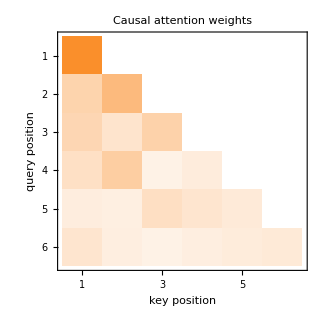

```mathematica
(* id: c4ac59d6-2cea-4822-ab8e-89524eb8cf8c · unit3_transformer · cell 8 of 24 · updated 2026-11-24 06:58 UTC *)
n = 6; q6 = RandomReal[{-1, 1}, {n, 4}]; k6 = RandomReal[{-1, 1}, {n, 4}]; v6 = RandomReal[{-1, 1}, {n, 3}];
MatrixPlot[softmaxRows[q6 . Transpose[k6]/2. + causalMask[n]], ColorFunction -> (Blend[{White, RGBColor[0.98, 0.56, 0.17]}, #] &), ColorFunctionScaling -> False,
 FrameLabel -> {"query position", "key position"}, PlotLabel -> "Causal attention weights", ImageSize -> 320, ImagePadding -> {{50, 10}, {40, 30}}]
```

Fig. 3. Attention weights with a causal mask, for 6 positions. Everything above the diagonal is exactly 0: no position looks ahead.

```mathematica
(* id: cc499b62-7740-49d3-915e-c7f10702a57e · unit3_transformer · cell 9 of 24 · updated 2026-11-24 06:58 UTC *)
out6 = sdpa[q6, k6, v6, causalMask[n]];
k2 = k6; v2 = v6; k2[[5 ;;]] = RandomReal[{-1, 1}, {2, 4}]; v2[[5 ;;]] = RandomReal[{-1, 1}, {2, 3}];
{close[sdpa[q6, k2, v2, causalMask[n]][[;; 4]], out6[[;; 4]], 10^-12],
 close[out6, AttentionLayer["Dot", "ScoreRescaling" -> "DimensionSqrt", "Mask" -> "Causal"][<|"Query" -> q6, "Key" -> k6, "Value" -> v6|>]],
 close[sdpa[q6, k6, v6, padMask[n, n, 4]], sdpa[q6, k2, v2, padMask[n, n, 4]], 10^-12]}
```

{True,True,True}

Check: {True, True, True}. Changing positions 5 and 6 leaves outputs 1–4 unchanged; the array mask equals AttentionLayer with "Mask" -> "Causal"; with 4 real keys, changing the 2 padding keys changes nothing. In Wolfram, padding needs no mask: sequences of different lengths are "Varying" dimensions, and NetTrain pads and masks them itself.

## 6. Multi-head attention

One attention with dmodel-dimensional queries is replaced by h attentions of dₖ = dmodel/h dimensions each, on different learned projections. Their outputs are joined and projected once more (Section 3.2.2):

MultiHead(Q, K, V) = Concat(head₁, …, headₕ) Wᴼ,      headᵢ = Attention(Q Wᵢ^Q, K Wᵢ^K, V Wᵢ^V)

As a Wolfram net, mhaNet uses LinearLayer for the projections (all heads at once), ReshapeLayer to split the dmodel features into h groups of dₖ, AttentionLayer with "MultiHead" -> True for the h attentions, FlattenLayer to join them and a last LinearLayer for Wᴼ.

In the base model dmodel = 512 and h = 8, so each head works in dₖ = 64 dimensions. The four projections Q, K, V and Wᴼ are 512 × 512 matrices with 512 biases each: 4 × (512.b2 + 512) = 4 × 262 656 = 1 050 624 parameters, whatever the number of heads.

```mathematica
(* id: a11dc73b-abfd-4695-b4e5-5f36ec4dede2 · unit3_transformer · cell 10 of 24 · updated 2026-11-24 06:58 UTC *)
net = NetInitialize@mhaNet[16, 4]; netc = NetInitialize@mhaNet[16, 4, True];
x = RandomReal[{-1, 1}, {5, 16}]; m = RandomReal[{-1, 1}, {7, 16}];
{close[net[<|"Query" -> x, "Memory" -> m|>], mha[net, {}, 4][x, m]], close[netc[<|"Query" -> x, "Memory" -> x|>], mha[netc, {}, 4, True][x, x]],
 Information[net, "ArraysTotalElementCount"] == mhaParams[16] == Information[NetInitialize@mhaNet[16, 1], "ArraysTotalElementCount"], mhaParams[512]}
```

{True,True,True,1050624}

Check: {True, True, True, 1050624}. The net from primitive layers equals multi-head attention from arrays (d = 16, h = 4), also with the causal mask; 4(d.b2 + d) parameters, the same for 1 head as for 4; 1 050 624 for the base model.

## 7. Positional encoding

Attention by itself ignores word order, so a position code is added to each embedding (Section 3.5). Each pair of components is a sine and a cosine of the position, with wavelengths from 2π to 10000 · 2π:

PE(pos, 2i) = sin(pos / 10000^(2i/dmodel)),      PE(pos, 2i+1) = cos(pos / 10000^(2i/dmodel))

Take dmodel = 4 and pos = 1. For i = 0 the frequency is 1: PE = (sin 1, cos 1) = (0.8415, 0.5403). For i = 1 it is 1/10000^(2/4) = 0.01: PE = (sin 0.01, cos 0.01) = (0.0100, 0.99995). So PE(1) = (0.8415, 0.5403, 0.0100, 0.99995): fast components tell nearby positions apart, slow ones tell distant ones apart.

```mathematica
(* id: 30046458-8fdb-49d4-9290-85a27840fee6 · unit3_transformer · cell 11 of 24 · updated 2026-11-24 06:58 UTC *)
pe[2, 4][[2]]
```

{0.841471,0.540302,0.00999983,0.99995}

Check: {0.8415, 0.5403, 0.0100, 0.99995}.

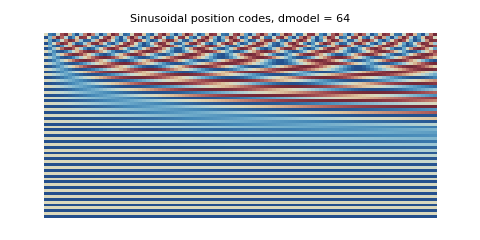

```mathematica
(* id: 0ebca81f-8b8d-4565-8c0c-522cbfbc3c9a · unit3_transformer · cell 12 of 24 · updated 2026-11-24 06:58 UTC *)
ArrayPlot[Transpose[pe[100, 64]], ColorFunction -> "RedBlueTones", FrameLabel -> {"dimension", "position"}, PlotLabel -> "Sinusoidal position codes, dmodel = 64",
 ImageSize -> 480, AspectRatio -> 0.5, ImagePadding -> {{50, 10}, {40, 30}}]
```

Fig. 4. The position code of positions 0–99 (across) in 64 dimensions (down). The first dimensions oscillate fast, the last ones hardly change.

The reason given for sinusoids: for every offset k there is one fixed matrix Mₖ, a rotation in each pair of components, with PE(pos + k) = Mₖ PE(pos) for every position. So “k places later” is a linear operation the net can learn.

```mathematica
(* id: 84461cb2-72ba-4407-9e5d-8f03e6428a6d · unit3_transformer · cell 13 of 24 · updated 2026-11-24 06:58 UTC *)
p100 = pe[100, 64];
{AllTrue[{1, 5, 17}, Function[s, close[Transpose[shiftMatrix[s, 64] . Transpose[p100[[1 ;; 100 - s]]]], p100[[1 + s ;; 100]], 10^-9]]],
 With[{dd = Table[p100[[p]] . p100[[p + 7]], {p, 1, 90}]}, Max[dd] - Min[dd] < 10^-9],
 With[{pn = NetInitialize@peNet[64], xx = RandomReal[{-1, 1}, {12, 64}]}, close[pn[xx], xx + pe[12, 64]] && close[pn[xx[[;; 3]]], xx[[;; 3]] + pe[3, 64]]]}
```

{True,True,True}

Check: {True, True, True}. One rotation per offset (k = 1, 5, 17); PE(pos)·PE(pos + 7) is the same for every pos, so it depends only on the distance; and peNet (SequenceIndicesLayer, a frozen LinearLayer, Sin) adds exactly these codes for any length. Frozen means LearningRateMultipliers -> 0.

## 8. Feed-forward, residual and LayerNorm

After attention, every position goes through the same two-layer network on its own: dmodel → dff → dmodel with a ReLU between (dff = 2048 in the base model; Section 3.3). Every sub-layer is wrapped in a residual connection and followed by layer normalisation (Section 3.1):

FFN(x) = max(0, x W₁ + b₁) W₂ + b₂          output = LayerNorm(x + Sublayer(x))          LayerNorm(v) = γ (v − mean v) / √(var v + ε) + β

The residual lets the signal and its gradient pass straight through. The normalisation keeps every position’s vector at mean 0 and variance 1 before a learned scale γ and shift β.

LayerNorm of v = (1, 2, 3) with γ = 1, β = 0: the mean is 2 and the variance (1 + 0 + 1)/3 = 2/3. With ε = 0.001, √(2/3 + 0.001) = 0.8171, so the result is (−1, 0, 1)/0.8171 = (−1.2238, 0, 1.2238). Without ε it would be ±1.2247.

```mathematica
(* id: bb20ad9b-f806-4841-91d7-3475a605dbe3 · unit3_transformer · cell 14 of 24 · updated 2026-11-24 06:58 UTC *)
lnTest = NetInitialize[NormalizationLayer[2, 2, "Input" -> {1, 3}]];
{lnTest[{{1., 2., 3.}}], NetExtract[lnTest, "Epsilon"]}
```

{{{-1.22383,0.,1.22383}},0.001}

Check: {{−1.2238, 0, 1.2238}}, ε = 0.001. Wolfram’s NormalizationLayer[2, 2] is LayerNorm over each position’s features, with ε = 0.001.

```mathematica
(* id: 5d1ee476-5ae7-46a5-8000-97563de85888 · unit3_transformer · cell 15 of 24 · updated 2026-11-24 06:58 UTC *)
fn = NetInitialize@ffnNet[16, 64]; xf = RandomReal[{-1, 1}, {5, 16}];
ln = NetReplacePart[NetInitialize[NormalizationLayer[2, 2, "Input" -> {5, 8}]], {"Scaling" -> RandomReal[{0.5, 1.5}, 8], "Biases" -> RandomReal[{-0.2, 0.2}, 8]}];
xl = RandomReal[{-2, 2}, {5, 8}];
{close[fn[xf], ffn[fn, {}][xf]], close[ln[xl], layerNorm[ln, {}][xl], 10^-4]}
```

{True,True}

Check: {True, True}: ffnNet equals the formula at every position, and NormalizationLayer equals LayerNorm from arrays with a random γ and β. The paper normalises after the residual sum (post-norm); many later transformers normalise before the sub-layer (pre-norm), which is easier to train when there are many layers.

## 9. One encoder layer and one decoder layer

An encoder layer is self-attention, then the feed-forward network, each wrapped as LayerNorm(x + Sublayer(x)). A decoder layer has three sub-layers: causal self-attention over the output so far, attention over the encoder’s output (queries from the decoder, keys and values from the encoder) and the feed-forward network (Fig. 1).

```mathematica
(* id: fe75b7f0-3908-49cd-ac1e-75f9022ef498 · unit3_transformer · cell 16 of 24 · updated 2026-11-24 06:58 UTC *)
enc = NetInitialize@encoderLayerNet[16, 4, 32]; dec = NetInitialize@decoderLayerNet[16, 4, 32];
xs = RandomReal[{-1, 1}, {6, 16}]; ys = RandomReal[{-1, 1}, {4, 16}]; mem = enc[xs];
{close[mem, encoderLayer[enc, 4][xs], 10^-4], close[dec[<|"Input" -> ys, "Memory" -> mem|>], decoderLayer[dec, 4][ys, mem], 10^-4],
 With[{ys2 = ReplacePart[ys, 4 -> RandomReal[{-1, 1}, 16]]}, close[dec[<|"Input" -> ys, "Memory" -> mem|>][[;; 3]], dec[<|"Input" -> ys2, "Memory" -> mem|>][[;; 3]], 10^-5]]}
```

{True,True,True}

Check: {True, True, True}. Both layer nets equal their array versions, and the decoder is causal: output i does not change when a later output position changes.

## 10. Shared embeddings, multiplied by √dmodel

The paper uses one weight matrix for the input embedding, the output embedding and the projection before the softmax, and multiplies the embeddings by √dmodel (Section 3.4). In Wolfram the sharing is NetSharedArray: EmbeddingLayer stores a V × d matrix, and LinearLayer[V] on d-dimensional inputs stores a V × d matrix too, so one array serves both.

```mathematica
(* id: 20b14262-9197-4db5-83d8-9fabfe93cf74 · unit3_transformer · cell 17 of 24 · updated 2026-11-24 06:58 UTC *)
shared = NetInitialize@NetGraph[<|"emb" -> EmbeddingLayer[8, 20, "Weights" -> NetSharedArray["W"]], "scale" -> ElementwiseLayer[Evaluate[Sqrt[8.]] # &],
    "out" -> NetMapOperator[LinearLayer[20, "Weights" -> NetSharedArray["W"]]]|>, {"emb" -> "scale" -> "out"}, "Input" -> {"Varying", Restricted["Integer", 20]}];
{Normal@NetExtract[shared, {"emb", "Weights"}] == Normal@NetExtract[shared, {"out", "Net", "Weights"}], Information[shared, "ArraysTotalElementCount"]}
```

{True,180}

Check: {True, 180}: the embedding and the output projection are one array, stored once: 20 × 8 = 160 shared weights and 20 output biases.

## 11. Label smoothing

The training target is not one-hot. With ε = 0.1 and K classes it puts 1 − ε + ε/K on the right class and ε/K on each of the others. The model learns to be less sure; the paper reports that this hurts perplexity but improves accuracy and BLEU (Section 5.4).

q = (1 − ε) onehot(y) + ε/K ,        loss = − Σₖ qₖ log pₖ

K = 4, right class 3, ε = 0.1: q = (0.025, 0.025, 0.925, 0.025). If the model predicts q itself the loss is −(0.925 ln 0.925 + 3 × 0.025 ln 0.025) = 0.0721 + 0.2767 = 0.349. If it is 99.9 % sure of class 3, the three small classes cost 0.075 × ln(3/0.001) ≈ 0.075 × 8.01 = 0.601, and the total is 0.601: being too sure is now penalised.

```mathematica
(* id: a8bcc671-aa9c-48e5-bc9a-b25a234af8d2 · unit3_transformer · cell 18 of 24 · updated 2026-11-24 06:58 UTC *)
{smoothTarget[3, 4], crossEntropy[smoothTarget[3, 4], smoothTarget[3, 4]], crossEntropy[smoothTarget[3, 4], {1/3000., 1/3000., 0.999, 1/3000.}]}
```

{{0.025,0.025,0.925,0.025},0.34878,0.601403}

Check: {{0.025, 0.025, 0.925, 0.025}, 0.349, 0.601}.

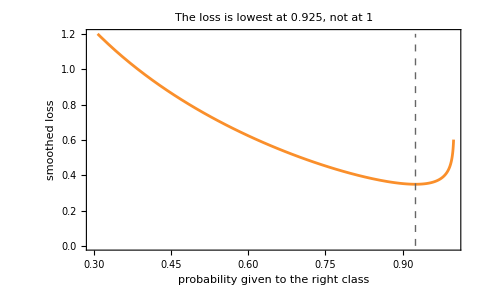

```mathematica
(* id: 60337b95-5479-4613-94ea-a49f7ee1ea97 · unit3_transformer · cell 19 of 24 · updated 2026-11-24 06:58 UTC *)
Plot[crossEntropy[smoothTarget[3, 4], Join[ConstantArray[(1 - s)/3, 2], {s}, {(1 - s)/3}]], {s, 0.3, 0.999}, PlotStyle -> RGBColor[0.98, 0.56, 0.17],
 Epilog -> {Dashed, GrayLevel[0.4], Line[{{0.925, 0}, {0.925, 1.2}}]}, PlotRange -> {0, 1.2},
 Frame -> True, FrameLabel -> {"probability given to the right class", "smoothed loss"}, PlotLabel -> "The loss is lowest at 0.925, not at 1", ImageSize -> 480, ImagePadding -> {{60, 10}, {40, 30}}]
```

Fig. 5. The label-smoothed loss for K = 4 as a function of the probability given to the right class (the rest shared equally). Its minimum is at 1 − ε + ε/K = 0.925 (dashed).

## 12. The warm-up learning-rate schedule

Adam with β₁ = 0.9, β₂ = 0.98, ε = 10⁻⁹. The learning rate rises linearly for the first 4000 steps, then falls as 1/√step (Section 5.3). The warm-up protects the young network from large, badly aimed steps.

lrate = dmodel^(−0.5) · min(step^(−0.5), step · warmup^(−1.5)),      warmup = 4000

The two terms are equal when step^(−0.5) = step · 4000^(−1.5), that is at step = 4000. There the rate is 512^(−0.5) × 4000^(−0.5) = 0.04419 × 0.01581 = 6.99 × 10⁻⁴, the peak.

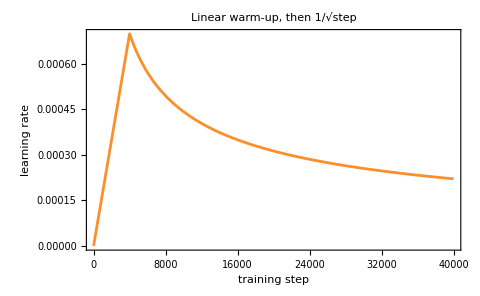

```mathematica
(* id: 123449f9-7c38-4bc4-8b54-d7e613274fdb · unit3_transformer · cell 20 of 24 · updated 2026-11-24 06:58 UTC *)
Plot[warmRate[s], {s, 1, 40000}, PlotStyle -> RGBColor[0.98, 0.56, 0.17], PlotRange -> All, Frame -> True, FrameLabel -> {"training step", "learning rate"},
 PlotLabel -> "Linear warm-up, then 1/√step", ImageSize -> 480, ImagePadding -> {{70, 10}, {40, 30}}]
```

Fig. 6. The learning rate over the first 40 000 steps.

```mathematica
(* id: 5382fdff-d5d5-4bcc-9f70-983b4c4be719 · unit3_transformer · cell 21 of 24 · updated 2026-11-24 06:58 UTC *)
{warmRate[4000], warmRate[3999] < warmRate[4000] > warmRate[4001]}
```

{0.000698771,True}

Check: {0.000699, True}. In Wolfram: NetTrain[…, Method -> {"ADAM", "Beta1" -> 0.9, "Beta2" -> 0.98, "LearningRate" -> peak, "LearningRateSchedule" -> (warmRate[#]/peak &)}]; the schedule is a factor of the learning rate. Unit 4 does this.

## 13. Beam search with a length penalty

Unit 1’s beam search keeps the B best partial outputs. Its scores are sums of log-probabilities, which only fall as a hypothesis grows, so plain beam search prefers short outputs. The paper uses beam size 4 and divides each finished hypothesis’s log-probability by a length penalty with α = 0.6 (Section 6.1, from Wu et al. 2016):

score(Y) = log P(Y | X) / lp(Y),        lp(Y) = ((5 + |Y|) / 6)^α

A short hypothesis with log P = −2.0 and 2 tokens, a long one with −2.6 and 8 tokens. Without the penalty the short one wins (−2.0 > −2.6). With α = 0.6: lp(2) = (7/6)^0.6 = 1.097 and lp(8) = (13/6)^0.6 = 1.590, so the scores are −2.0/1.097 = −1.823 and −2.6/1.590 = −1.635. Now the long one wins.

```mathematica
(* id: 7355bb5e-cc11-4f14-9895-8dc51848c4c4 · unit3_transformer · cell 22 of 24 · updated 2026-11-24 06:58 UTC *)
{lengthPenalty[2], lengthPenalty[8], -2.0/lengthPenalty[2], -2.6/lengthPenalty[8]}
```

{1.0969,1.59029,-1.82332,-1.63493}

Check: {1.097, 1.590, −1.823, −1.635}.

## 14. How big is the base model?

Counted from the parts above, for dmodel = 512, dff = 2048, h = 8, 6 encoder and 6 decoder layers and the shared vocabulary of about 37 000 tokens (Section 5.1).

Attention: 4(512.b2 + 512) = 1 050 624. Feed-forward: 512 × 2048 + 2048 + 2048 × 512 + 512 = 2 099 712. LayerNorm: 2 × 512 = 1024. An encoder layer has 1 050 624 + 2 099 712 + 2 × 1024 = 3 152 384, a decoder layer 2 × 1 050 624 + 2 099 712 + 3 × 1024 = 4 204 032. Six of each: 18 914 304 + 25 224 192 = 44 138 496. The shared embedding adds 37 000 × 512 = 18 944 000 and the softmax biases 37 000. Total 63 119 496, within 3 % of the 65M of the paper’s Table 3.

```mathematica
(* id: 803f29e0-8edb-4473-89bc-9082ef18c47c · unit3_transformer · cell 23 of 24 · updated 2026-11-24 06:58 UTC *)
With[{p = layerParams[512, 2048]}, {p, 6 (p["attention"] + p["FFN"] + 2 p["LayerNorm"]) + 6 (2 p["attention"] + p["FFN"] + 3 p["LayerNorm"]) + 37000*512 + 37000,
  With[{q = layerParams[16, 32]}, Information[enc, "ArraysTotalElementCount"] == q["attention"] + q["FFN"] + 2 q["LayerNorm"] &&
    Information[dec, "ArraysTotalElementCount"] == 2 q["attention"] + q["FFN"] + 3 q["LayerNorm"]]}]
```

{<|attention→1050624,FFN→2099712,LayerNorm→1024|>,63119496,True}

Check: the three per-layer counts, the total 63 119 496, and True: the per-layer formulas agree with Wolfram’s counts for the small layers of §9. The exact total depends on the vocabulary and on what is counted.

## 15. Exercises

1. Repeat §3.1 with q = (2, 0). Does the output move towards v₁ or away from it?

2. With dₖ = 16 and no scaling, what is the standard deviation of q·k?

3. Compute PE(2) for dmodel = 4 by hand.

4. With K = 10 and ε = 0.1, what probability does the smoothed target give the right class?

5. At which step is the learning rate of §12 half its peak, after the peak?

Answers, computed:

```mathematica
(* id: 2354defa-7813-484c-81af-baf3956c113d · unit3_transformer · cell 24 of 24 · updated 2026-11-24 06:58 UTC *)
{sdpa[{{2., 0.}}, {{1., 0.}, {0., 1.}}, {{1., 0.}, {0., 1.}}], Sqrt[16.], pe[3, 4][[3]], smoothTarget[1, 10][[1]],
 s /. FindRoot[warmRate[s] == warmRate[4000]/2, {s, 10000}]}
```

{{{0.80443,0.19557}},4.,{0.909297,-0.416147,0.0199987,0.9998},0.91,16000.}

1: (0.804, 0.196): a better match gives more weight to v₁. 2: 4. 3: (sin 2, cos 2, sin 0.02, cos 0.02) = (0.909, −0.416, 0.020, 0.9998). 4: 0.91. 5: step 16 000, since the rate falls as 1/√step.

## 16. Summary

Attention is a weighted average: softmax(QKᵀ/√dₖ)V, where the √dₖ keeps the softmax from saturating. Masks decide who may look at whom. Several heads attend in different subspaces for the price of one. Sinusoidal codes add order in a way that makes shifts linear. Each sub-layer is wrapped as LayerNorm(x + Sublayer(x)), and an encoder and a decoder layer are built from these parts alone. Shared embeddings, label smoothing, warm-up and a length penalty complete the recipe. Every part built from primitive Wolfram layers equals its array version.

Next: Unit 4 assembles these nets into a transformer that expands ⨂/⨁ expressions, and trains it.

© 2026 Computational Classnotes · CC BY-NC-SA 4.0